# Calculating 2nd Order G0Σ (p, τ) for BEC Polaron

## Parameters and Equations

```mathematica
SetDirectory["/home/h/H.Guertner/theorie/BEC_Polaron/Mathematica/"];
<<params.mx
```

## Integrating τ1 , τ2 and τ3

```mathematica
Integrand[q1_,q2_,τ_,τ1_, τ2_,τ3_ ,costheta_] := 1/(2*Pi)^6*vq2[q1]*vq2[q2]*g0[0,tbeg, τ1]*dq[q1,τ1,τ]* dq[q2,τ2,τ3]*g0[q1,τ1,τ2]*g0[q1,τ3,τ]*g0cos[q1,q2,τ2,τ3, costheta];
```

### Plot of final Integrand for q Integral

```mathematica
f[q1_,q2_,τ_,τ2_,τ3_, costheta_]:=Integrate[Integrand[q1,q2,τ,τ1,τ2, τ3, costheta],  {τ1,0,τ2}];
g[q1_,q2_,τ_,τ3_, costheta_]:=Integrate[f[q1,q2,τ,τ2, τ3, costheta],{τ2,0,τ3}];
h[q1_,q2_,τ_,costheta_]:=Integrate[g[q1,q2,τ, τ3, costheta],{τ3,0,τ}];
```

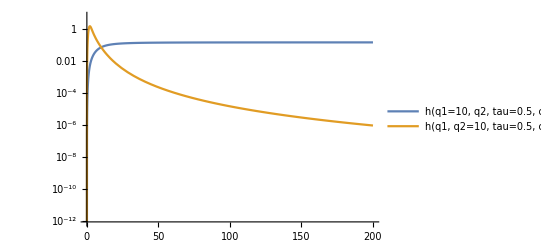

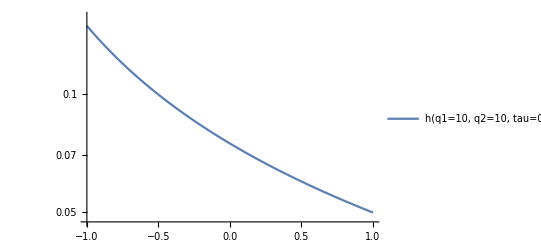

```mathematica
hplot1=LogPlot[{4*Pi*10^2*2*Pi*q^2*h[10,q,0.5, 0],4*Pi*q^2*2*Pi*10^2* h[q,10,0.5,0]},{q,0,qc}, PlotLegends -> {"h(q1=10, q2, tau=0.5, costheta=0)", "h(q1, q2=10, tau=0.5, costheta=0)"}]
hplot2 =LogPlot[4*Pi*10^2*2*Pi*10^2*h[10,10,0.5, t],{t,-1,1}, PlotLegends -> {"h(q1=10, q2=10, tau=0.5, costheta)"}]
```

## Q Integral

### Q2 Integral in sphere coordinates with theta Integral

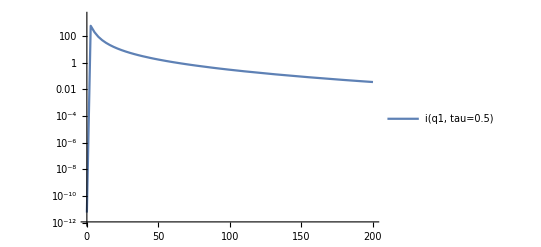

```mathematica
i[q1_,τ_]:=NIntegrate[2*Pi*q2^2*h[q1,q2,τ, costheta],{costheta,-1,1},{q2,0,qc} ];
iplot=LogPlot[4*Pi*q^2*i[q,0.5],{q,0,qc},  PlotPoints->10, MaxRecursion->3, PlotRange->Full,PlotLegends -> {"i(q1, tau=0.5)"}]
```

### Q1 Integral in sphere coordinates

```mathematica
g0se[τ_]:=NIntegrate[4*Pi*q1^2*2*Pi*q2^2*h[q1,q2,τ, costheta],{q1,0,qc},{costheta,-1,1},{q2,0,qc} ];
```

```mathematica
LogPlot[g0se[τ],{τ,0,8}, PlotPoints->10, MaxRecursion->4, PlotRange->Full, PlotLegends->"G0Se"]
```

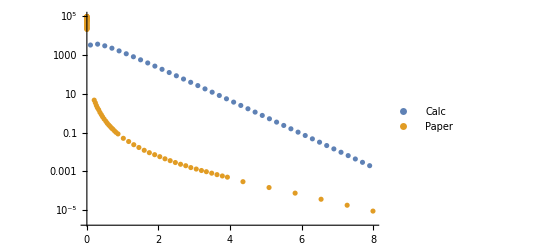

```mathematica
data = Table[{τ, g0se[τ]},{τ, 0.1, 8, 0.2}];
ListLogPlot[{data, paper},PlotLegends->{"Calc", "Paper"} ]
```

```mathematica
DumpSave["2nd_G0SE.mx", {iplot, hplot1,hplot2, data}];
Export["mat_2nd_g0se", data, "Table"];
```

## Laplace Transform to Σ2 (p=0, ω)

```mathematica
<<2nd_SEw.mx;
```

```mathematica
LaplaceData = Table[{ω,NIntegrate[4*Pi*q1^2*2*Pi*q2^2*h[q1,q2,τ, costheta]* Exp[ω*τ]/(-g0pw[0,ω,0]),{q1,0,qc},{costheta,-1,1},{q2,0,qc} ,{τ,0,Infinity}]},{ω,-100,-1, 5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{-100,41.1745},{-95,42.4562},{-90,43.8422},{-85,45.347},{-80,46.9885},{-75,48.7883},{-70,50.7731},{-65,52.9764},{-60,55.4408},{-55,58.2214},{-50,61.3912},{-45,65.049},{-40,69.3326},{-35,74.441},{-30,80.6748},{-25,88.5144},{-20,98.7862},{-15,113.073},{-10,134.916},{-5,174.783}}

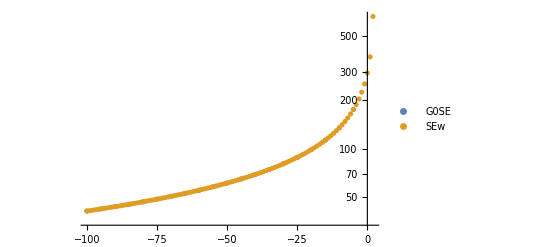

```mathematica
ListLogPlot[{LaplaceData, Σ2omegadata}, PlotLegends -> {"G0SE", "SEw"}]
```